I am trying to search for still lifes in Conways game of life

An object in Conways Game of Life can be represented by an array of Booleans, say, of size w h

A still life is a stable object, so it needs to satisfy the following conditions.

Condition 1.

For each living cell, the number of its living neighbors must be 2 or 3

For each dead cell, the number of its living neighbors must not be 3.

Written in Mathematica code, these are

```mathematica
Clear[k,i,j,b];
k=1;
i=j=1;


neighborCount[k_,{i_,j_}]:=BooleanCountingFunction[{k},Delete[Catenate[Array[b,{3,3},{i,j}-1]],5]];

neighborCount[2,{i,j}]
```

(b[0,0]&&b[0,1]&&!b[0,2]&&!b[1,0]&&!b[1,2]&&!b[2,0]&&!b[2,1]&&!b[2,2])||(b[0,0]&&!b[0,1]&&b[0,2]&&!b[1,0]&&!b[1,2]&&!b[2,0]&&!b[2,1]&&!b[2,2])||(b[0,0]&&!b[0,1]&&!b[0,2]&&b[1,0]&&!b[1,2]&&!b[2,0]&&!b[2,1]&&!b[2,2])||(b[0,0]&&!b[0,1]&&!b[0,2]&&!b[1,0]&&b[1,2]&&!b[2,0]&&!b[2,1]&&!b[2,2])||(b[0,0]&&!b[0,1]&&!b[0,2]&&!b[1,0]&&!b[1,2]&&b[2,0]&&!b[2,1]&&!b[2,2])||(b[0,0]&&!b[0,1]&&!b[0,2]&&!b[1,0]&&!b[1,2]&&!b[2,0]&&b[2,1]&&!b[2,2])||(b[0,0]&&!b[0,1]&&!b[0,2]&&!b[1,0]&&!b[1,2]&&!b[2,0]&&!b[2,1]&&b[2,2])||(!b[0,0]&&b[0,1]&&b[0,2]&&!b[1,0]&&!b[1,2]&&!b[2,0]&&!b[2,1]&&!b[2,2])||(!b[0,0]&&b[0,1]&&!b[0,2]&&b[1,0]&&!b[1,2]&&!b[2,0]&&!b[2,1]&&!b[2,2])||(!b[0,0]&&b[0,1]&&!b[0,2]&&!b[1,0]&&b[1,2]&&!b[2,0]&&!b[2,1]&&!b[2,2])||(!b[0,0]&&b[0,1]&&!b[0,2]&&!b[1,0]&&!b[1,2]&&b[2,0]&&!b[2,1]&&!b[2,2])||(!b[0,0]&&b[0,1]&&!b[0,2]&&!b[1,0]&&!b[1,2]&&!b[2,0]&&b[2,1]&&!b[2,2])||(!b[0,0]&&b[0,1]&&!b[0,2]&&!b[1,0]&&!b[1,2]&&!b[2,0]&&!b[2,1]&&b[2,2])||(!b[0,0]&&!b[0,1]&&b[0,2]&&b[1,0]&&!b[1,2]&&!b[2,0]&&!b[2,1]&&!b[2,2])||(!b[0,0]&&!b[0,1]&&b[0,2]&&!b[1,0]&&b[1,2]&&!b[2,0]&&!b[2,1]&&!b[2,2])||(!b[0,0]&&!b[0,1]&&b[0,2]&&!b[1,0]&&!b[1,2]&&b[2,0]&&!b[2,1]&&!b[2,2])||(!b[0,0]&&!b[0,1]&&b[0,2]&&!b[1,0]&&!b[1,2]&&!b[2,0]&&b[2,1]&&!b[2,2])||(!b[0,0]&&!b[0,1]&&b[0,2]&&!b[1,0]&&!b[1,2]&&!b[2,0]&&!b[2,1]&&b[2,2])||(!b[0,0]&&!b[0,1]&&!b[0,2]&&b[1,0]&&b[1,2]&&!b[2,0]&&!b[2,1]&&!b[2,2])||(!b[0,0]&&!b[0,1]&&!b[0,2]&&b[1,0]&&!b[1,2]&&b[2,0]&&!b[2,1]&&!b[2,2])||(!b[0,0]&&!b[0,1]&&!b[0,2]&&b[1,0]&&!b[1,2]&&!b[2,0]&&b[2,1]&&!b[2,2])||(!b[0,0]&&!b[0,1]&&!b[0,2]&&b[1,0]&&!b[1,2]&&!b[2,0]&&!b[2,1]&&b[2,2])||(!b[0,0]&&!b[0,1]&&!b[0,2]&&!b[1,0]&&b[1,2]&&b[2,0]&&!b[2,1]&&!b[2,2])||(!b[0,0]&&!b[0,1]&&!b[0,2]&&!b[1,0]&&b[1,2]&&!b[2,0]&&b[2,1]&&!b[2,2])||(!b[0,0]&&!b[0,1]&&!b[0,2]&&!b[1,0]&&b[1,2]&&!b[2,0]&&!b[2,1]&&b[2,2])||(!b[0,0]&&!b[0,1]&&!b[0,2]&&!b[1,0]&&!b[1,2]&&b[2,0]&&b[2,1]&&!b[2,2])||(!b[0,0]&&!b[0,1]&&!b[0,2]&&!b[1,0]&&!b[1,2]&&b[2,0]&&!b[2,1]&&b[2,2])||(!b[0,0]&&!b[0,1]&&!b[0,2]&&!b[1,0]&&!b[1,2]&&!b[2,0]&&b[2,1]&&b[2,2])

```mathematica
life44
```

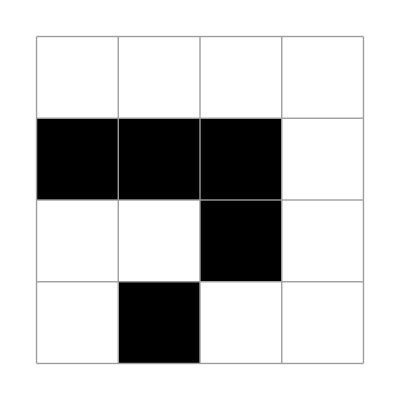
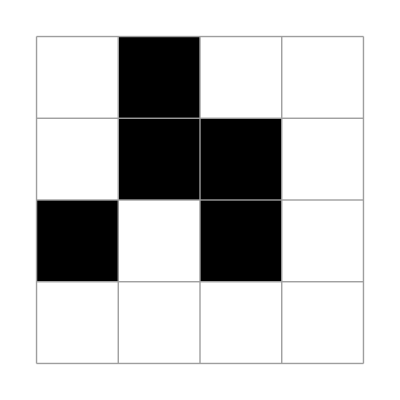
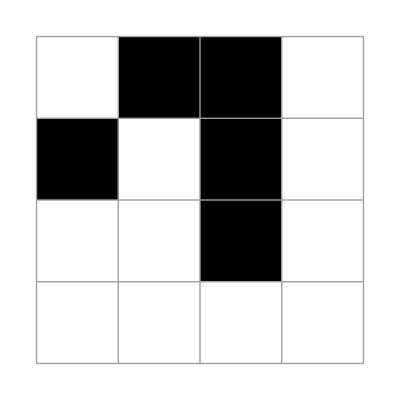
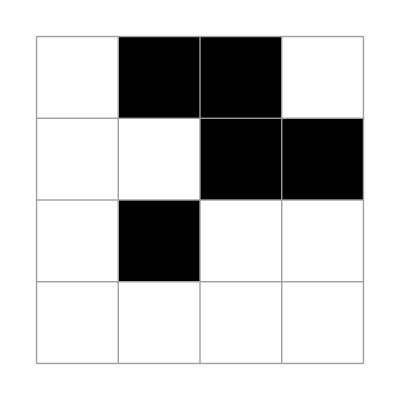

```mathematica
X1=({{0, 0, 0, 0}, {1, 1, 1, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}});
plt/@NestList[updateLife[{4,4}][ #]&,
X1,3]
```